# NV-center qubits

## This virtual quantum device is inspired by devices reported by the Delft team

## VQD setup

Set the main directory as the current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink package
One may also use the off-line questlink.m file, change it to the location of the local file

```mathematica
Import["https://qtechtheory.org/questlink.m"]
```

This will download a binary file  quest_link if there is no such file found
Otherwise, use a locally-compiled that called quest_link*

```mathematica
(* Search for existing files that match the pattern "quest_link*" *)
With[{questLinkFiles=Sort@FileNames["quest_link*",{NotebookDirectory[]}]}
,
If[Length[questLinkFiles]>0,
(* If one or more matching files are found, use the first one alphabetically *)
Print["Using the existing link file: ",First@questLinkFiles];
CreateLocalQuESTEnv[First@questLinkFiles];
,
(*If no matching files are found, download the link file*)
Print["No link file found, download quest_link"];
CreateDownloadedQuESTEnv[];
];
]
```

Load the VQD package; must be loaded after QuESTlink is loaded

```mathematica
Get["../vqd.wl"]
```

## User device configuration

Qubit 0 indicates electron spin,and the rest are nuclear spins  C^13 and N^14 - if applicable
Time unit is second (s)
Frequency unit is  Hertz (Hz)

```mathematica
Options[NVCenterDelft]={
QubitNum->6
,
(* T1 of each qubit *)
T1-> <|0-> 3600,1->60,2->60,3->60,4->60,5->60 |>
,
(* T2 of each qubit; we assume dynamical decoupling is actively applied *)
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9,5->9|>
,
(* dipolar interaction among nuclear spins: cross-talk ZZ-coupling in order of a few Hz on passive noise *)
FreqWeakZZ->5
,
(* direct single rotation on Nuclear spin is done via RF, put electron in state -1 leave out the Rx Ry on nuclear spins ideally. *)
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500,5->500|>
,
(* usually done virtually *)
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3,5->400*10^3|>
,
(* Frequency of CRot gate, conditional rotation done via dynamical decoupling or dd+RF. The gate is conditioned on electron spin state *)
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 ,5->2*10^3|>
,
(* Fidelity of CRot gate  *)
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98 ,5->0.98|>
,
(* fidelity of x- and y- rotations on each qubit *)
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99,5->0.99 |>
,
(* fidelity of z- rotations on each qubit *)
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999,4->0.999,6->0.99 |>
,
(* Error ratio of 1-qubit depolarising:dephasing of x- and y- rotations  *)
EFSingleXY->{0.75,0.25}
,
(* Error ratio of 2-qubit depolarising:dephasing of CRot gate *)
EFCRot->{0.9,0.1}
,
(* initialization fidelity on the electron spin *)
FidInit-> 0.999
,
(* initialization duration on the electron spin *)
DurInit->2*10^-3
,
(* measurement fidelity on the electron spin *)
FidMeas->0.946
,
(* measurement duration on the electron spin *)
DurMeas->2*10^-5
};
```

## Elementary guide

### Native gates

Direct iIitialisation and measurement are on the NV electron spin only
Init_0, M_0

Single-qubit gates
Rx_q[θ], Ry_q[θ], Rz_q[θ] 

Two-qubit gates are conditional rotation, where  CRσ[θ]:=|0X0|⊗ Rσ[θ]+|1X1|⊗ Rσ[-θ]
CRx_(0,q)[θ], CRy_(0,q)[θ]

others: doing nothing
Wait_q[duration]

### Common nuclear spin gates, obtained by sequence of native gates

```mathematica
(* cotrolled-pauli gates, where control qubits are the electron spins *)
Subscript[cX, c_,t_] := Sequence @@ {Subscript[CRx, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Rx, t][-π/2]}
Subscript[cY, c_,t_] := Sequence @@ {Subscript[CRy, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][-π/2]}
Subscript[cZ, c_,t_] := Sequence @@ {Subscript[Rx, t][π/2],Subscript[CRy, c,t][-π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][π/2],Subscript[Rx, t][-π/2]}
(* initialisation the nuclear spins *)
Subscript[initNcl, q_ /; q>0] :=Sequence @@ {Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[CRx, 0,q][π/2],Subscript[Rx, 0][π/2],Subscript[CRy, 0,q][-π/2]}
(*measurement sequences on nuclear spins the computational basis *)
Subscript[measZ, q_ /; q>0] := Sequence[Subscript[Ry, 0][π/2],Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Rx, 0][π/2],Subscript[M, 0]]
```

{Init_0,Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2]}

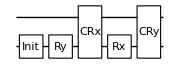

```mathematica
{Subscript[initNcl, 1]}
DrawCircuit@%
```

### Example: 6 Qubits initialization

Initialize all qubits to zero

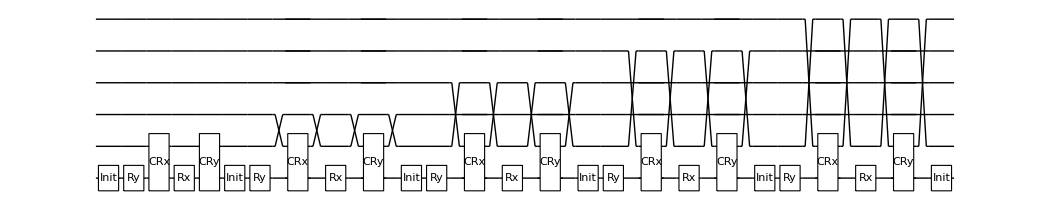

```mathematica
circInit={Subscript[initNcl, 1],Subscript[initNcl, 2],Subscript[initNcl, 3],Subscript[initNcl, 4],Subscript[initNcl, 5],Subscript[Init, 0]};
DrawCircuit[circInit]
```

```mathematica
ρ=CreateDensityQureg[6];
ρ2=CreateDensityQureg[6];
ψ=CreateQureg[6];
```

First, create a random mix state. Notice that the fidelity is far from 000000

```mathematica
SetQuregMatrix[ρ, RandomMixState[6]];
CalcFidelity[ρ, InitZeroState @ ψ]
```

0.0149238

Initialization on the noisy circuit. Serialize[circ] removes parallelism in the circuit.
In practice, the operators are done in serial manner while dynamical-decoupling sequences are applied to passive qubits (qubits that are not operated upon)

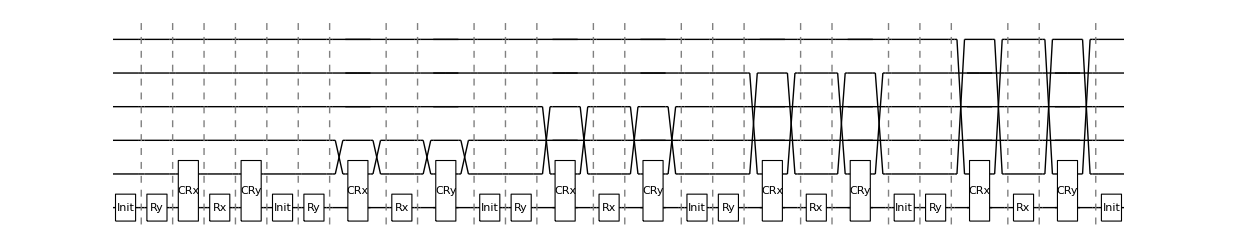

```mathematica
DrawCircuit@Serialize@circInit
```

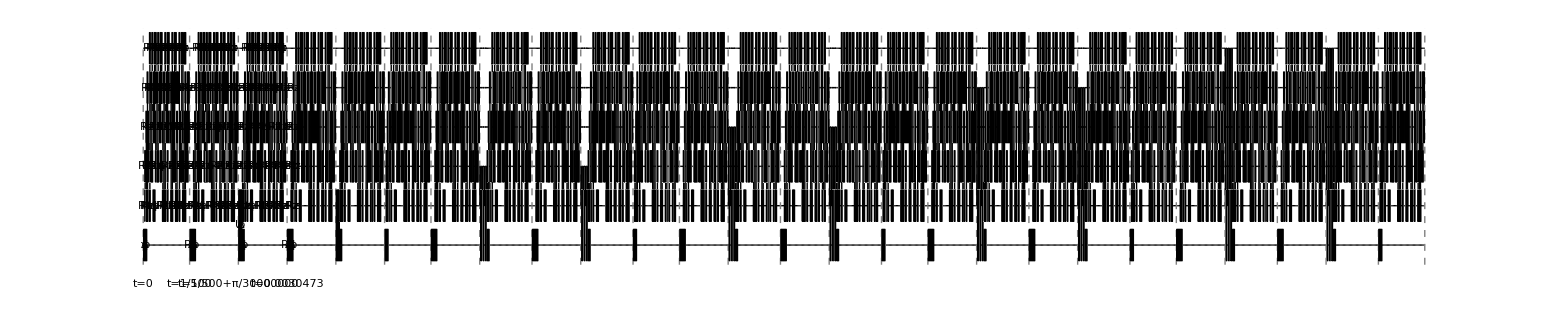

```mathematica
(* 
noisy initialisation circuit on the specified device 
*)
circInitOnDev=InsertCircuitNoise[Serialize @ circInit, NVCenterDelft[], ReplaceAliases->True];
DrawCircuit[%,6]
```

The fidelity is now so closer to the state 000000

```mathematica
ApplyCircuit[CloneQureg[ρ2,ρ],ExtractCircuit @ circInitOnDev];
CalcFidelity[ρ2, InitZeroState @ ψ]
```

0.932412

```mathematica
DestroyAllQuregs[]
```

### Measurements

Measurements in the computational basis. Compare 4k shots of measurement to the fidelity set in the device

```mathematica
nshots=1000;
{ρ,ρinit}=CreateDensityQuregs[6,2];
```

#### On the electron spin

```mathematica
outputs=
Flatten @ Table[
ApplyCircuit[InitZeroState @ ρ,ExtractCircuit @ InsertCircuitNoise[{Subscript[M, 0]},NVCenterDelft[],ReplaceAliases->True]]
,
{nshots}
];
	Print["correct outputs(0):"<>ToString[nshots - Total @ outputs],  "\nflipped outputs(1):"<>ToString[Total @ outputs],"\nfidelity:"<>ToString[N[1 - Total @ outputs/nshots] 100]]
```

correct outputs(0):943
flipped outputs(1):57
fidelity:94.3

Compare it to the targeted fidelity of measurement

```mathematica
OptionValue[NVCenterDelft,FidMeas]
```

0.946

#### Measurement on the nuclear spins

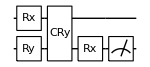

```mathematica
DrawCircuit[{Subscript[measZ, 1]}]
```

Should be worse than direct measurement on the electron spin, because it is an indirect measurement

```mathematica
dev=NVCenterDelft[];
```

```mathematica
nshots=1000;
outputs=Flatten@Table[
ApplyCircuit[InitZeroState@ρ,ExtractCircuit@InsertCircuitNoise[{Subscript[measZ, 1]},NVCenterDelft[],ReplaceAliases->True]],{nshots}];
Print["correct outputs(0):"<>ToString[nshots-Total@outputs], "\nflipped outputs(1):"<>ToString[Total@outputs],"\nfidelity:"<>ToString[N[1-Total[outputs]/nshots]]]
```

correct outputs(0):943
flipped outputs(1):57
fidelity:0.943

## Paper supplement: BCS dynamic simulation

### Trotterization

It requires around one thousand gates -- before conversion to the native NV-gates. See supplement/BCSonVNCenterDelft/BCSDynamicsTrotter.nb

### BCS simulation

#### Setting up the hamiltonian

Set the constants for the hamiltonian

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
}
```

{t1→(9 ℏ)/J,t2→(18 ℏ)/J,Γ→0.1,ω→(5 J)/3}

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire Hamiltonain

```mathematica
(* Gaudin term *)
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
(* Subscript[H, BCS] *)
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Set up the time discretisation and the quench g(τ)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20.,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

```mathematica
(*τ=t J/ℏ*)
```

```mathematica
(* dense quench for reference *)
gdense<<"supplement/BCSonNVCenterDelft/gdense.mx";
```

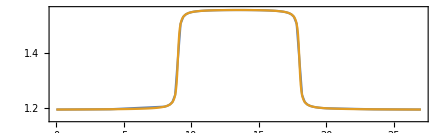

```mathematica
(* See the quench almost overlap with the discretised one *)
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[{Transpose@{τs,gvals},gdense},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

### Simulations on various noise scenarios

```mathematica
summarycss2<<"supplement/BCSonNVCenterDelft/summarycss2.mx";
```

```mathematica
CustomGatesDefinitions={Subscript[SW, index1_,index2_][θ_]:>Subscript[U, index1,index2][{{1,0,0,0},{0,ⅇ^((ⅈ θ)/2)Cos[θ/2],-ⅈ ⅇ^((ⅈ θ)/2)Sin[θ/2],0 },{0,-ⅈ ⅇ^((ⅈ θ)/2)Sin[θ/2], ⅇ^((ⅈ θ)/2)Cos[θ/2],0 },{0,0,0,1}}]
,
Subscript[CRx, e_,n_][θ_]:>Subscript[U, e,n][{{Cos[θ/2],0,-I Sin[θ/2],0},{0,Cos[θ/2],0,I Sin[θ/2]},{-I Sin[θ/2],0,Cos[θ/2],0},{0,I Sin[θ/2],0,Cos[θ/2]}}]
,
	Subscript[CRy, e_,n_][θ_]:>Subscript[U, e,n][{{Cos[θ/2],0,-Sin[θ/2],0},{0,Cos[θ/2],0,Sin[θ/2]},{Sin[θ/2],0,Cos[θ/2],0},{0,-Sin[θ/2],0,Cos[θ/2]}}]	
}; 
CustomGatesDraw={Subscript[SW, index1_,index2_][_]:>Subscript[SWAP, index1,index2]};
```

```mathematica
noisyBCS[ρ_,ρinit_,ψinit_,vdopt_:{}]:=Module[{τ,rexactnoisy,noisycirc,fid},
τ = 0;
CloneQureg[ρ,ρinit];
rexactnoisy = {{0,1}};
Table[
noisycirc = ExtractCircuit @ InsertCircuitNoise[List /@ sum["circnvc"], NVCenterDelft[Sequence @@ vdopt]];
noisycirc = DeleteCases[DeleteCases[noisycirc,Subscript[__, __][0.]] ,Subscript[__, __][0]];
ApplyCircuit[ρ, noisycirc/.CustomGatesDefinitions];
fid = CalcFidelity[ρ, ψinit];
τ += sum["δ"];
AppendTo[rexactnoisy, {τ, fid}];
(*<|"τ"->τ,"δ"->sum["δ"],"fidnoisy"->fid,"ϵnoisy"->Abs[sum["fidexact"]-fid]|>*)
,{sum,  summarycss2}];
rexactnoisy
]
```

## A realistic setting of virtual NV-center device -- inspired from the paper

```mathematica
Options[NVCenterDelft]={
QubitNum->5
,
T1-> <|0-> 3600,1->60,2->60,3->60,4->60 |>
,
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9|>
,
FreqWeakZZ->5
,
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500|>
,
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3|>
,
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 |>
,
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98|>
,
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99 |>
,
FidSingleZ->  <| 0->1,1-> 1,2->1, 3->1,4->1 |>
,
EFSingleXY->{0.75,0.25}
,
EFCRot->{0.9,0.1}
,
FidInit-> 0.999
,
DurInit->2*10^-3
,
FidMeas->0.946
,
DurMeas->2*10^-5
};
```

Several tested error scenarios -- these can be flexibly changed/added :

1)  Exact unitary using MatrixExp[]
2) Checking using the resulting CSS compilation
3) Realistic numbers from Mohammed 
4) Perfect gates with realistic decoherence
5) Extremely high gates fidelity 99.999, realistic decoherence
6) 10x longer decoherece with excellent gates 99.999

```mathematica
labels=<|
1->"Exact propagator",
2->"Subspace compilation",
3->"Realistic noise",
4->"Gates fidelity 99.999, no cross-talk",
5->"Gates fidelity 99.999",
6->"10x of T1,T2",
7->"Gates fidelity 99.999, 10x of T1,T2",
8->"Gates fidelity 99.999, 10x of T1,T2, no cross-talk"
|>;
```

```mathematica
(* 
Prepare initialisation state in ψinit as an exact groundstate from Subscript[H, BCS]
*)
DestroyAllQuregs[];
ψinit=CreateQureg[5];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
initmat=(List/@initv).Conjugate[{initv}];
{ρ,ρinit}=CreateDensityQuregs[5,2];
SetQuregMatrix[ρinit,initmat];
SetQuregMatrix[ψinit,initv];
```

```mathematica
(* 
Load other data for result comparison: 
exact propagator,
  approximation by compilation in the subspace and converted to the native NVC gates
*)
rexactot2<<"supplement/BCSonNVCenterDelft/rexactot2.mx"
rexactcompcss<<"supplement/BCSonNVCenterDelft/rexactcompcss.mx"
```

Null rexactot2

Null rexactcompcss

The main execution on scaling the noise

```mathematica
(* 
Here are some options used
 optgates: set all qubits fidelity to 99.999
optdec: set all decoherece T1 and T2 to 10x longer
*)
optgates = {FidCRot -> Association[{# -> .99999} & /@ Range[4]], FidSingleXY -> Association[{# -> .99999} & /@ Range[0, 4]]};
optdec = {T1 -> <|0 -> 36000, 1 -> 600, 2 -> 600, 3 -> 600, 4 -> 600 |>, T2 -> <|0 -> 15, 1 -> 100, 2 -> 100, 3 -> 100, 4 -> 90|>};

(*
The main execution: notice that we can just change the options. Feel free to change/add here
*)
bcsfidelities = <|
   1 -> rexactot2,
   2 -> rexactcompcss,
   3 -> noisyBCS[ρ, ρinit, ψinit],
   4 -> noisyBCS[ρ, ρinit, ψinit, Join[optgates,{FreqWeakZZ->False}]],
   5 -> noisyBCS[ρ, ρinit, ψinit, optgates],
   6 -> noisyBCS[ρ, ρinit, ψinit, optdec],
   7 -> noisyBCS[ρ, ρinit, ψinit, Join[optgates, optdec]],
   8 -> noisyBCS[ρ, ρinit, ψinit, Join[optgates, optdec, {FreqWeakZZ -> False}]]
   |>;
```

```mathematica
plotstyles={PlotRange->All,
PlotTheme->"Scientific",
AspectRatio->.6,
Background->White,
ImageSize->600,
Frame->True,
FrameStyle->Directive[Thick,Black,17],
BaseStyle->{16},
GridLines->{τs,None},
GridLinesStyle->Directive[GrayLevel[0.8,0.8],Thin]
};
```

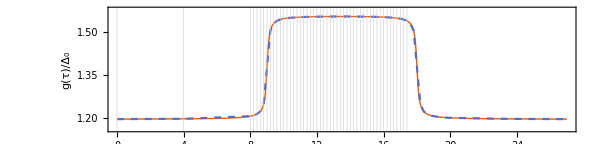

```mathematica
(*  
Beautiful plot for the quench potential 
*)
keys={"analytic","discretised"};
bcs1=ListPlot[
{gdense,Transpose@{τs,gvals}},
PlotRange->{1.16,1.58},
Joined->{True,True},
AspectRatio->0.24,
PlotStyle->{Thick,Dashed},
PlotLegends->Placed[LineLegend[keys,Spacings->0],{.15,.25}],
FrameLabel->{{"g(τ)/Δ_0",None},{None,None}},
ImagePadding->{{58,10},{0,0}},
Sequence@@plotstyles]
```

The compilation outputs for a reference

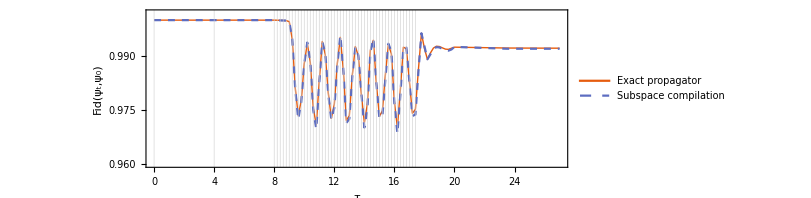

```mathematica
keys={1,2};
bcs2=ListPlot[
bcsfidelities/@keys,
Joined->ConstantArray[True,Length@keys],
PlotStyle->Join[{Thick},ConstantArray[Dashed,Length@keys-1]],
PlotLegends->Placed[LineLegend[labels/@keys,Spacings->0],{.22,.2}],
PlotRange->{Automatic,{0.96,1.002}},
AspectRatio->.33,
ImagePadding->{{58,10},{50,0}},
FrameLabel->{"τ","Fid(ψ_t,ψ_0)"},
Sequence@@plotstyles
]
```

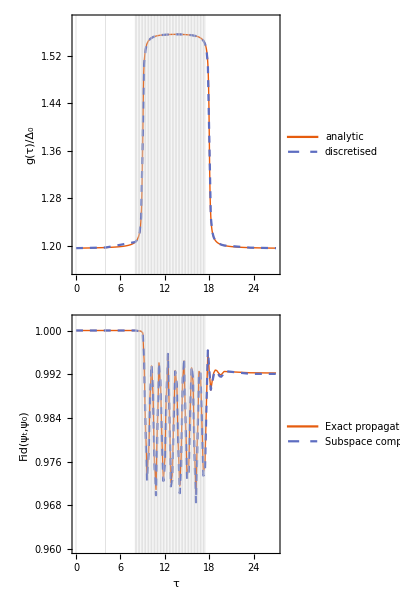

```mathematica
Column[{bcs1,bcs2},Spacings->-0.1]
(*Export["quench.pdf",%]*)
```

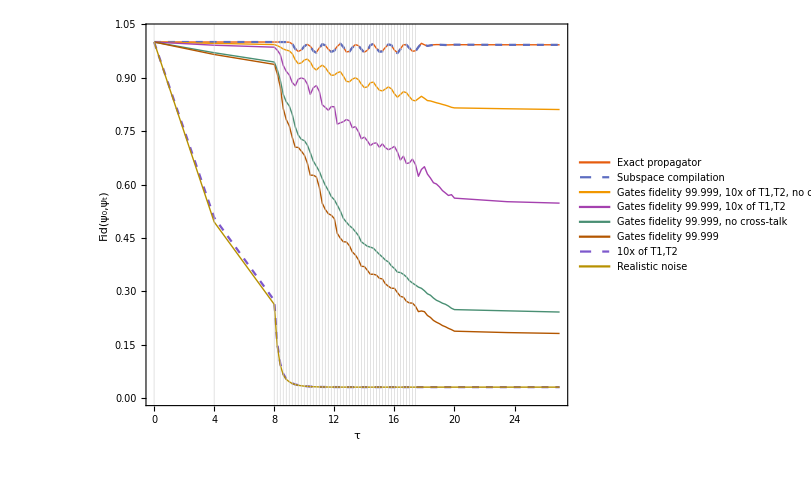

```mathematica
(*
The final plot after various trials 
*)
keys={1,2,8,7,4,5,6,3};
bcs3=ListPlot[
bcsfidelities/@keys,
Joined->ConstantArray[True,Length@bcsfidelities],
PlotStyle->{Thick,Dashed,Thick,Thick,Thick,Thick,Dashed,Thick},
AspectRatio->0.8,
PlotLegends->Placed[LineLegend[labels/@keys,Spacings->0,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0]&)],
{0.4,0.2}],
ImagePadding->{{58,10},{50,0}},
FrameLabel->{"τ","Fid(ψ_0,ψ_t)"},
PlotRange->{{0,27},{0.0,1.03}},
BaseStyle->{14},
Sequence@@plotstyles
]
(*Export["bcsall.pdf",%]*)
```